## Accelerated Trajectories Back and Forth

```mathematica
Clear[a]
```

```mathematica
z[τ_,a_,x0_,t0_,τ0_]:={t0+1/a Sinh[a (τ-τ0)],(x0-1/a)+1/a Cosh[a (τ-τ0)]}
```

These are two patches of Rindler Trajectories back and forth, which accelerate from proper time τ  = -T to τ = T:

```mathematica
γ1[τ_,a_,T_]:=z[τ,a,-1/a,0,0];
γ2[τ_,a_,T_] := z[τ,-a,-1/a+2/a Cos[a T],2/a Sinh[a T],2 T]
```

The function below is not working well with Piecewise, but it would be neat if it worked like this:

```mathematica
γ[τ_,a_,T_]:=Piecewise[{{z[τ,a,-1/a,0,0],-T<=τ&& τ<= T},{z[τ,-a,-1/a+2/a Cos[a T],2/a Sinh[a T],2 T],T<τ&& τ<=3 T}}]
```

The function below integrates I^- for the two pieces of Rindler trajectories:

```mathematica
int[Ω_,k_,a_,T_]:=NIntegrate[ⅇ^(ⅈ Ω τ - ⅈ k γ1[τ,a,T]⟦1⟧ + ⅈ k γ1[τ,a,T]⟦2⟧),{τ,-T,T}]+NIntegrate[ⅇ^(ⅈ Ω τ - ⅈ k γ2[τ,a,T]⟦1⟧ + ⅈ k γ2[τ,a,T]⟦2⟧),{τ,T,3T}]
```

The function below concatenates n of these trajectories, and adds the resulting I^-:

```mathematica
intN[Ω_,k_,a_,T_,n_]:=Sum[NIntegrate[ⅇ^(ⅈ Ω τ - ⅈ k z[τ,a,-1/a,(4i)/a Sinh[a T],4i T]⟦1⟧ + ⅈ k z[τ,a,-1/a,(4i)/a Sinh[a T],4i T]⟦2⟧),{τ,4i T-T,4i T +T}]+NIntegrate[ⅇ^(ⅈ Ω τ - ⅈ k  z[τ,-a,-1/a+2/a Cos[a T],(4i+2)/a Sinh[a T],4 i T+2 T]⟦1⟧ + ⅈ k  z[τ,-a,-1/a+2/a Cos[a T],(4i+2)/a Sinh[a T],4 i T+2 T]⟦2⟧),{τ,4i T +T,4i T +3T}],{i,0,n,1}]
```

Let us first see what happens for some parameters in the case of one back-and-forth cycle. The convention for all the plots is that blue represents I^- and yellow represents I^+. Notice that in order to obtain |I^+|, it is enough to change Ω to -Ω in I^-. We will set T = 1, which implies that all quantities are dimensionalized by T.

```mathematica
Dynamic[k]
```

```mathematica
ta1m = Table[{k,Abs[int[2,k,2,1]]},{k,0,10,0.01}];
```

```mathematica
ta1p = Table[{k,Abs[int[-2,k,2,1]]},{k,0,10,0.01}];
```

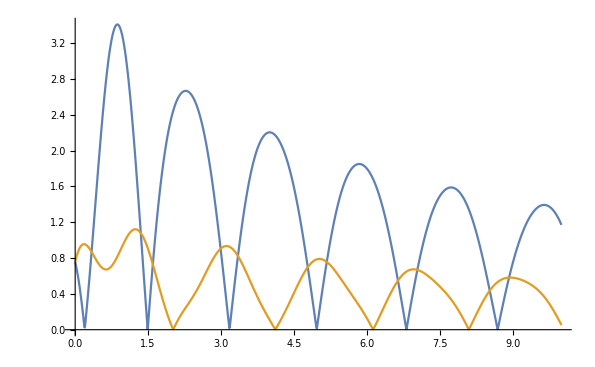

```mathematica
ListPlot[{ta1m,ta1p},Joined->True,PlotRange->All]
```

This is great! We can find parameters such that I^+=0 and I^-!=0 :)

Let us play with other parameters as well. Decreasing Ω gives:

```mathematica
Dynamic[k]
```

```mathematica
ta2m = Table[{k,Abs[int[1,k,2,1]]},{k,0,10,0.01}];
```

```mathematica
ta2p = Table[{k,Abs[int[-1,k,2,1]]},{k,0,10,0.01}];
```

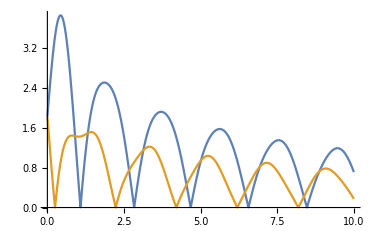

```mathematica
ListPlot[{ta2m,ta2p},Joined->True,PlotRange->All]
```

which seems slightly worse than the previous parameters.

Let us try to increase Ω instead:

```mathematica
Dynamic[k]
```

```mathematica
ta3m = Table[{k,Abs[int[3,k,2,1]]},{k,0,10,0.01}];
```

```mathematica
ta3p = Table[{k,Abs[int[-3,k,2,1]]},{k,0,10,0.01}];
```

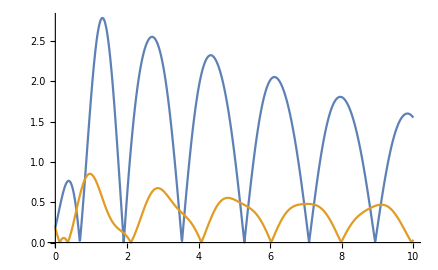

```mathematica
ListPlot[{ta3m,ta3p},Joined->True,PlotRange->All]
```

This seems to increase the relative size of I^- with respect to I^+ :/

If we decrease the acceleration we get:

```mathematica
Dynamic[k]
```

```mathematica
ta4m = Table[{k,Abs[int[2,k,1,1]]},{k,0,10,0.01}];
```

```mathematica
ta4p = Table[{k,Abs[int[-2,k,1,1]]},{k,0,10,0.01}];
```

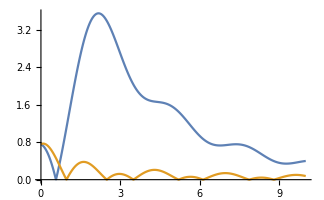

```mathematica
ListPlot[{ta4m,ta4p},Joined->True,PlotRange->All]
```

which we do not like at all!

So what if we also decrease the gap?

```mathematica
Dynamic[k]
```

```mathematica
ta5m = Table[{k,Abs[int[1,k,1,1]]},{k,0,10,0.01}];
```

```mathematica
ta5p = Table[{k,Abs[int[-1,k,1,1]]},{k,0,10,0.01}];
```

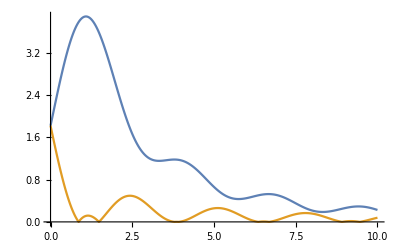

```mathematica
ListPlot[{ta5m,ta5p},Joined->True,PlotRange->All]
```

Not good either.

Now, let us start looking at more cycles. It is a good idea to keep the good parameters that we first found. For 2 cycles, we find:

```mathematica
ta1mN = Table[{k,Abs[intN[2,k,2,1,1]]},{k,0,10,0.01}];
```

```mathematica
ta1pN = Table[{k,Abs[intN[-2,k,2,1,1]]},{k,0,10,0.01}];
```

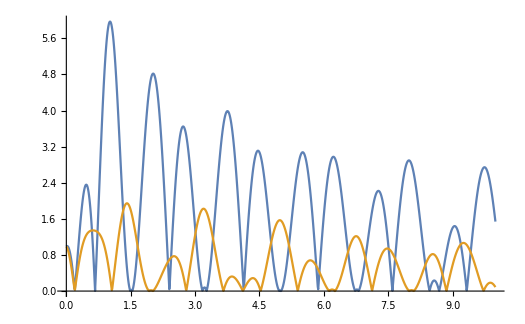

```mathematica
ListPlot[{ta1mN,ta1pN},Joined->True,PlotRange->All]
```

It seems that the plot above also has I^+ = 0 where the previous one was zero. To make sure, let us plot both below (dashed = 2 cycles, solid = 1 cycle):

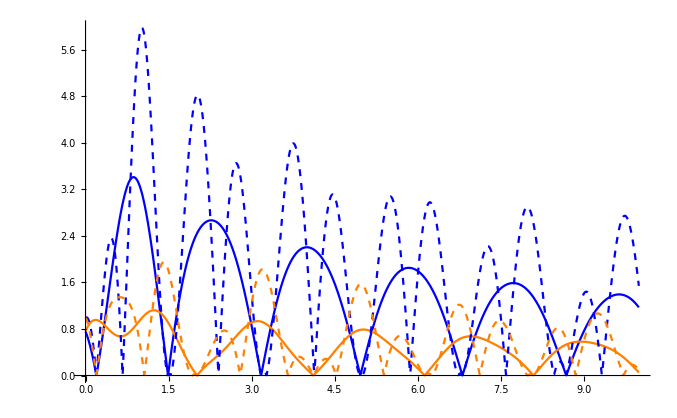

```mathematica
ListPlot[{ta1m,ta1p,ta1mN,ta1pN},Joined->True,PlotRange->All,PlotStyle->{Blue,Orange,{Blue,Dashed},{Orange,Dashed}}]
```

Now we can see that the zeros that we found for I^+ after one cycle are also zeros for two cycles.

Let us now try three cycles:

```mathematica
ta1mN2 = Table[{k,Abs[intN[2,k,2,1,2]]},{k,0,10,0.01}];
```

```mathematica
ta1pN2 = Table[{k,Abs[intN[-2,k,2,1,2]]},{k,0,10,0.01}];
```

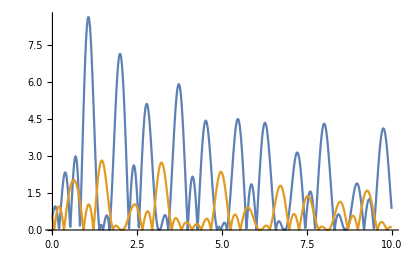

```mathematica
ListPlot[{ta1mN2,ta1pN2},Joined->True,PlotRange->All]
```

This has a lot of oscillations, so it is hard to tell whether it also has the same zeros as before. Let us plot one, two and three cycles in the same plot (dotted = 3 cycles, dashed = 2 cycles, solid = 1 cycle):

```mathematica
ListPlot[{ta1m,ta1p,ta1mN,ta1pN,ta1mN2,ta1pN2},Joined->True,PlotRange->All,PlotStyle->{Blue,Orange,{Blue,Dashed},{Orange,Dashed},{Blue,Dotted},{Orange,Dotted}},Ticks->{{π/2,π,3π/2,2π,5π/2},Automatic}]
```

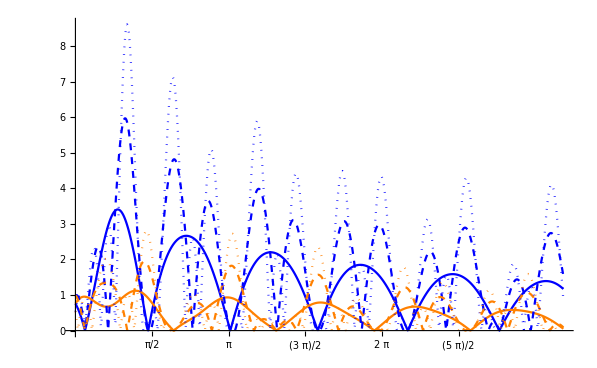

We found again that the zeros of I^+ after one cycle are also zeros after two and three cycles! This is great! We can now ask someone to build a cavity with the eigenfrequencies equal to the values of k where I^+ = 0 for one cycle, and our whole transparency idea works. Moreover, this is indeed acceleration induced transparency!
The values of π/2, π, (3π)/2,... in the plot above mean nothing, I was just wondering whether the zeros coincided with these values, but they don’t.

With the parameters picked, we would have Ω = (2ℏ)/T, a = (2c)/T for the parameter T picked. If, for instance, the atoms were accelerated for T = 1s in their proper time, so that each cycle lasts for 4s, we would have a = 6 10^8 m/s^2. This gives an Unruh temperature of the order of 10^-20 K, which means that thermalization to the Unruh temperature is not an issue at all for us.